```mathematica
tmax=5;
soln=DSolve[{x''[t]+x'[t]/t-8(1-delta1)(1+x[t])==0,x[tmax]==-1},x[t],t];
Simplify[soln]
```

{{x[t]→-1+BesselJ[0,2 ⅈ √(2-2 delta1) t] C[1]-(BesselJ[0,10 ⅈ √(2-2 delta1)] BesselY[0,-2 ⅈ √(2-2 delta1) t] C[1])/BesselY[0,-10 ⅈ √(2-2 delta1)]}}

1

0.1

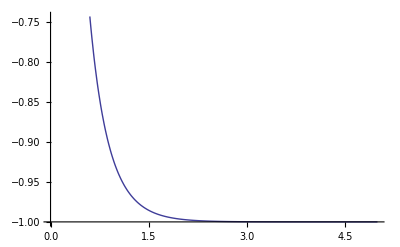

```mathematica
phi[t_]:=coef(Sqrt[t]*Exp[2 √(2-2 delta1)t])^-1-1
coef=1
delta1=0.1
Plot[phi[t],{t,0,5}]
```

```mathematica
Clear[coef,delta1]
```

```mathematica
eq=phi'[t]/.coef->("phi[t]"+1)(Sqrt[t]*Exp[2 √(2-2 delta1)t]);
Simplify[eq]
phi'[t]==eq;
```

-((1+phi[t]) (1+4 √(2-2 delta1) t))/(2 t)

```mathematica
tmax=5;
soln=DSolve[{y''[t]+y'[t]/t-2(3delta2/4-4)(1+y[t])/(1+gamma)==0,y[tmax]==-1},y[t],t];
Simplify[soln]
```

{{y[t]→-1+BesselJ[0,(ⅈ √(-8+(3 delta2)/2) t)/(√(1+gamma))] C[1]-(BesselJ[0,(5 ⅈ √(-8+(3 delta2)/2))/(√(1+gamma))] BesselY[0,-(ⅈ √(-8+(3 delta2)/2) t)/(√(1+gamma))] C[1])/BesselY[0,-(5 ⅈ √(-8+(3 delta2)/2))/(√(1+gamma))]}}

```mathematica
chi[t_]:=coef2 (Sqrt[t]*Exp[(√(-8+(3 delta2)/2) t)/(√(1+gamma))])^-1-1
eq2=phi'[t]/.coef->("psi[t]"+1)(Sqrt[t]*Exp[(√(-8+(3 delta2)/2) t)/(√(1+gamma))])
chi[t]
```

-2 (1+psi[t]) √(2-2 delta1) ⅇ^(-2 √(2-2 delta1) t+(√(-8+(3 delta2)/2) t)/(√(1+gamma)))-((1+psi[t]) ⅇ^(-2 √(2-2 delta1) t+(√(-8+(3 delta2)/2) t)/(√(1+gamma))))/(2 t)

-1+(coef2 ⅇ^(-(√(-8+(3 delta2)/2) t)/(√(1+gamma))))/(√t)

```mathematica
D[Sech[x],x]
```

-Sech[x] Tanh[x]